Mod[1/6+x,1/3]

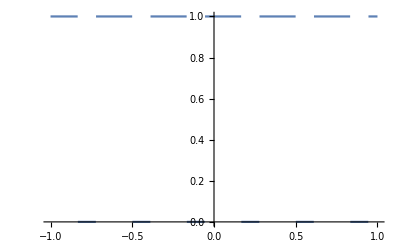

Mod[π/3+x,1/3]

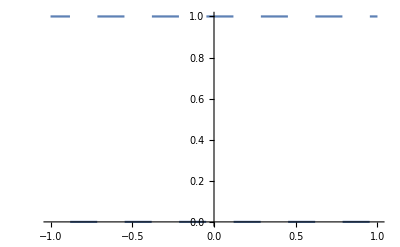

```mathematica
ClearAll[x,y];
y[x_]=Mod[x+1/6,1/3]
Plot[Piecewise[{{1,y[x]>1/9&&y[x]<1/3}}],{x,-1,1}]
z[x_]=Mod[x+Pi/3,1/3]
Plot[Piecewise[{{1,z[x]<1/6}}],{x,-1,1}]
```